```mathematica
b[p1_,p2_,pd1_,pd2_,pd3_] :=-12+12  *p1+12  *p2+3  *pd1+3  *pd2+4 * pd3;
c[p1_,p2_,pd1_,pd2_,pd3_] := 48-96 * p1+36  *p1^2-96  *p2+108 p1 * p2+36 * p2^2-24  *pd1+30 * p1  *pd1+18  *p2  *pd1-24 * pd2+18  *p1 * pd2+30 * p2 * pd2+8  *pd1  *pd2-32  *pd3+36  *p1 * pd3+36 * p2 * pd3+8 * pd1  *pd3+8 * pd2  *pd3;
d[p1_,p2_,pd1_,pd2_,pd3_] := -64+192 * p1-144  *p1^2+192 * p2-432  *p1  *p2+216 * p1^2 * p2-144  *p2^2+216 p1 p2^2+48 pd1-120 p1 pd1+72 p1^2 pd1-72 p2 pd1+108 p1 p2 pd1+48 pd2-72 p1 pd2-120 p2 pd2+108 p1 p2 pd2+72 p2^2 pd2-32 pd1 pd2+36 p1 pd1 pd2+36 p2 pd1 pd2+64 pd3-144 p1 pd3+72 p1^2 pd3-144 p2 pd3+144 p1 p2 pd3+72 p2^2 pd3-32 pd1 pd3+36 p1 pd1 pd3+36 p2 pd1 pd3-32 pd2 pd3+36 p1 pd2 pd3+36 p2 pd2 pd3;
```

```mathematica
p[p1_,p2_,pd1_,pd2_,pd3_]:=3 * c[p1,p2,pd1,pd2,pd3] - b[p1,p2, pd1,pd2,pd3]^2;
q[p1_,p2_,pd1_,pd2_,pd3_]:= d[p1,p2,pd1,pd2,pd3]- b[p1,p2,pd1,pd2,pd3]*c[p1,p2,pd1,pd2,pd3]/3+2 * b[p1,p2,pd1,pd2,pd3]^3/27;
Delta[p1_,p2_,pd1_,pd2_,pd3_]:=(q[p1,p2,pd1,pd2,pd3]/2)^2+(p[p1,p2,pd1,pd2,pd3]/3)^3;
```

```mathematica
Delta[0.1,0.1,0.1,0.1,0.1]
```

-0.00235191

0.0697236

0.0897215

0.00886445

0.0415269

-Graphics3D-

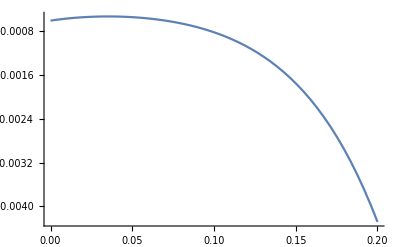

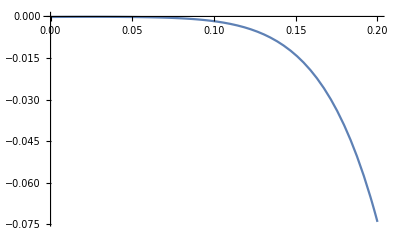

0

-1.87218×10^-9

-2.6×10^-11

-0.00146477

```mathematica
(*Random choose 3 values for p1,p2,pd1,pd2,pd3 and find the func associated to the other two inputs*)
r1 = RandomReal[]/10
r2 = RandomReal[]/10
r3 = RandomReal[]/10
r4 = RandomReal[]/10
Plot3D[Delta[ r1,r2,x, y,r3],{x,0,1},{y,0,1}]
Plot[Delta[r1,r2,r4,x,r3],{x,0,0.2}]
Plot[Delta[r1,x,r2,r4,r3],{x,0,0.2}]
Delta[0,0, 0,0,0]
Delta[0.01,0.01, 0.01,0,0.01]
Delta[0,0, 0,0.01,0]
```

```mathematica
RootEqOne[p1_,p2_,pd1_,pd2_,pd3_]:=b[p1,p2, pd1,pd2,pd3]*4 + c[p1,p2, pd1,pd2,pd3]+d[p1,p2, pd1,pd2,pd3]/4+16
(*One of root equals 4*)
```

```mathematica
r1 = RandomReal[]/10
r2 = RandomReal[]/10
r3 = RandomReal[]/10
r4 = RandomReal[]/10
RootEqOne[r1,r1,r1,r1, r1]
Plot3D[RootEqOne[0,x,0,0, y],{x,0,1},{y,0,1}]
RootEqOne[0,r1,r2,0, 0.0001]
RootEqOne[0,r1,r2,0, 0.0001]
RootEqOne[0,r1,r2,0, 0.0001]
```

0.029703

0.0790064

0.0250927

0.0607569

0.00849071

-Graphics3D-

3.70013×10^-6

3.70013×10^-6

3.70013×10^-6

```mathematica
f[p1_,p2_,pd1_,pd2_,pd3_]:=b[p1,p2, pd1,pd2,pd3]^2/4 - 2 * b[p1,p2, pd1,pd2,pd3]-12;
g[p1_,p2_,pd1_,pd2_,pd3_]:=-(b[p1,p2, pd1,pd2,pd3] + 4)^2
zeros[p1_,p2_,pd1_,pd2_,pd3_] := Abs[f[p1,p2,pd1,pd2,pd3]-c[p1,p2, pd1,pd2,pd3]]+Abs[g[p1,p2,pd1,pd2,pd3]-d[p1,p2, pd1,pd2,pd3]]
```

```mathematica
r1 = RandomReal[]/10
r2 = RandomReal[]/10
r3 = RandomReal[]/10
r4 = RandomReal[]/10
Plot3D[zeros[0,0, y,x, 0],{x,0.055,0.1},{y,0.055,0.1}]
zeros[0,0,x,r3, r4]
```

```mathematica
f[0,0,pd1, pd2,pd3] - c[0,0,pd1, pd2,pd3]
```

-60+24 pd1+24 pd2-8 pd1 pd2+32 pd3-8 pd1 pd3-8 pd2 pd3-2 (-12+3 pd1+3 pd2+4 pd3)+1/4 (-12+3 pd1+3 pd2+4 pd3)^2

```mathematica
Simplify[-60+24 pd1+24 pd2-8 pd1 pd2+32 pd3-8 pd1 pd3-8 pd2 pd3-2 (-12+3 pd1+3 pd2+4 pd3)+1/4 (-12+3 pd1+3 pd2+4 pd3)^2]
```

1/4 (9 pd1^2+9 pd2^2-8 pd2 pd3+16 pd3^2-2 pd1 (7 pd2+4 pd3))

```mathematica
Factor[1/4 (9 pd1^2+9 pd2^2-8 pd2 pd3+16 pd3^2-2 pd1 (7 pd2+4 pd3))]
```

1/4 (9 pd1^2-14 pd1 pd2+9 pd2^2-8 pd1 pd3-8 pd2 pd3+16 pd3^2)